Mathematica implementation of the Numerical Renormalization Group (NRG)
Rok Zitko, rok.zitko@theorie.physik.uni-goettingen.de, April 2008

```mathematica
<<sneg`sneg`;
```

sneg 1.188 Copyright (C) 2007 Rok Zitko

```mathematica
snegfermionoperators[d,f,g]
snegrealconstants[U,δ,Γ,γ]
```

```mathematica
bzc=qszbasis[{g[]}];MatrixForm[bzc]
qndiffs=bzc[[All,1]];
newstate[i_]:=bzc[[i,2,1]];
combs=Length[bzc];
```

({-1,0} | {1}
{0,-1/2} | {g_↓^†}
{0,1/2} | {g_↑^†}
{1,0} | {-g_↓^†·g_↑^†})

```mathematica
vev3[expr_]:=Module[{expr2},(*Note:there will always be only one f operator*)expr2=(expr/.nc->nc2)//.{nc2[a___,x1:f[__],x2:op_[__],b___]:>-nc2[a,x2,x1,b]/;fermionQ[op]};
expr2=expr2/.nc2[a__,x:f[__]]:>nc2[a] x;
expr2/.nc2[a__]:>vev[nc[a]]
];
matrixhop[i_,j_]:=matrixhop[i,j]=Module[{pdt},
pdt=nc[conj @ newstate[i],hop[f[],g[]],newstate[j]];
vev3[pdt]/.f[__]->1
];
{matrixhop[1,2],matrixhop[1,3],matrixhop[2,4],matrixhop[3,4]}
```

{1,1,-1,1}

```mathematica
recalcf[i_,j_,op_]:=braketop[newstate[i],op,newstate[j]];rftab[op_]:=Select[Flatten[Table[{i,j,recalcf[i,j,op]},{i,combs},{j,combs}],1],(#[[3]]!=0)&];
rfUP=rftab[g[CR,UP]]
rfDO=rftab[g[CR,DO]]
```

{{3,1,1},{4,2,1}}

{{2,1,1},{4,3,-1}}

```mathematica
Hd=δ(number[d]-1)+U/2 pow[number[d]-1,2]
Hc=Sqrt[γ]hop[f[],d[]]
H=Hc+Hd;
```

δ (-1+d_↓^†·d_↓^+d_↑^†·d_↑^)+1/2 U (1-d_↓^†·d_↓^-d_↑^†·d_↑^-2d_↓^†·d_↑^†·d_↓^·d_↑^)

√γ (d_↓^†·f_↓^+d_↑^†·f_↑^+f_↓^†·d_↓^+f_↑^†·d_↑^)

```mathematica
params={U->0.2,Γ->0.02,δ->0,γ->Γ Θ A[Λ]/π};
KEEP=400;
Λ=3;
faktor=2/(1+1/Λ);
SCALE[n_]=1/faktor Λ^-((n-1)/2);
Θ=2; (* Flat band *)
A[Λ_]=1/2 (1+1/Λ)/(1-1/Λ)Log[Λ];
```

```mathematica
Second[l_List]:=l[[2]];
ineachsubspace[l_,fnc_]:=Map[{First[#],fnc @ Second[#]}&,l];
showmatrices[l_]:=Print[MatrixForm @ ineachsubspace[l,MatrixForm]];
MyEigen=Composition[Transpose,Sort,Transpose,Eigensystem];
```

```mathematica
bz=qszbasisvc[{d[],f[]}];MatrixForm[bz]
subspaces[0]=bz[[All,1]];
showmatrices[makematricesbzvc[H,bz]]
Hrescaled=H  faktor/Sqrt[Λ];
hams[0]=makematricesbzvc[Hrescaled,bz]//.params;
```

({-2,0} | {‖▯▯▯▯⟩}
{-1,-1/2} | {‖▯▯▯▮⟩,‖▯▮▯▯⟩}
{-1,1/2} | {‖▯▯▮▯⟩,‖▮▯▯▯⟩}
{0,-1} | {‖▯▮▯▮⟩}
{0,0} | {‖▯▯▮▮⟩,‖▯▮▮▯⟩,‖▮▯▯▮⟩,‖▮▮▯▯⟩}
{0,1} | {‖▮▯▮▯⟩}
{1,-1/2} | {‖▯▮▮▮⟩,‖▮▮▯▮⟩}
{1,1/2} | {‖▮▯▮▮⟩,‖▮▮▮▯⟩}
{2,0} | {‖▮▮▮▮⟩})

({-2,0} | (1/2 (U-2 δ))
{-1,-1/2} | (1/2 (U-2 δ) | √γ
√γ | 0)
{-1,1/2} | (1/2 (U-2 δ) | √γ
√γ | 0)
{0,-1} | (0)
{0,0} | (1/2 (U-2 δ) | -√γ | √γ | 0
-√γ | 0 | 0 | -√γ
√γ | 0 | 0 | √γ
0 | -√γ | √γ | U/2+δ)
{0,1} | (0)
{1,-1/2} | (0 | -√γ
-√γ | U/2+δ)
{1,1/2} | (0 | -√γ
-√γ | U/2+δ)
{2,0} | (U/2+δ))

```mathematica
(* Note: negative n denotes the results after truncation! *)
truncn[n_]:=-n;
eig[n_]:=eig[n]=ineachsubspace[hams[n],MyEigen];
unshiftedenergies[n_]:=Sort@Flatten[eig[n] [[All,2,1]]];
Egs[n_]:=Egs[n]=First[unshiftedenergies[n]];
energies[n_]:=energies[n]=unshiftedenergies[n]-Egs[n];
```

```mathematica
(* Utility and accessor routines *)
nrsubs[n_]:=Length[subspaces[n]];
subsp[n_,i_Integer]:=subspaces[n][[i]];
ElementPosition[l_List,elem_]:=Position[l,elem,{1},1,Heads->False];
index[n_,subsp_List]:=ElementPosition[subspaces[n],subsp][[1,1]]
nrstates[n_]:=Sum[dimsub[n,i],{i,nrsubs[n]}];
dimsub[n,Null]:=0;
dimsub[n_,x_]:=Length[e[n,x]];
(* Eigenvalues *)
e[n_,Null]:={};
e[n_,i_Integer]:=eig[n][[i,2,1]]-Egs[n];
e[n_,subsp_List]:=e[n,index[n,subsp]];
(* Eigenvectors *)
U[n_,Null]:=NoMatrix;
U[n_,i_Integer]:=eig[n][[i,2,2]];
U[n_,subsp_List]:=U[n,index[n,subsp]];
(* Check for orthonormality of eigenvectors *)
check[n_]:=Module[{},
Print[ineachsubspace[eig[n],Det[Second[#]]&]//MatrixForm];
showmatrices[ineachsubspace[eig[n],Chop[Second[#].Transpose[Second[#]]]&]];
];
```

```mathematica
(* Calculate thermodynamic quantities *)
β=0.46;
Zsubsp[n_,i_]:=Total@Exp[-β e[n,i]];
Z[n_]:=Sum[Zsubsp[n,i],{i,nrsubs[n]}];
Sz2[n_]:=Sum[subsp[n,i][[2]]^2 Zsubsp[n,i],{i,nrsubs[n]}] /Z[n];
Sz[n_]:=Sum[subsp[n,i][[2]] Zsubsp[n,i],{i,nrsubs[n]}] /Z[n];
Q[n_]:=Sum[subsp[n,i][[1]] Zsubsp[n,i],{i,nrsubs[n]}] /Z[n];

calctd[n_]:=Module[{},
Print["nr. states=",nrstates[n]];
Print["Z=",Z[n]];
Print["Sz^2=",Sz2[n]];
Print["Sz=",Sz[n]];
Print["Q=",Q[n]]
];
```

```mathematica
rotate[n_,{subsp1_,subsp2_},matrix_]:=U[n,subsp1].matrix.Transpose[U[n,subsp2]];
ireduc[op_]:=Module[{l},
l=makeallmatricesbzvc[op,bz];
Apply[Function[{ss,m},{ss,rotate[0,ss,m]}],l,1]
];
(* Matrix elements of f operator *)
mf[0]=Join[ireduc[f[CR,UP]],ireduc[f[CR,DO]]];
(* Expectation value of a singlet operator *)
tracesub[n_,{{subsp_,subsp_},mat_}]:=Diagonal[mat].Exp[-β e[truncn[n],subsp]];
expv[n_,opx_]:=Total[Map[tracesub[n,#]&,mat[n,opx]]]/Z[truncn[n]];
```

```mathematica
opnd=number[d]
mat[0,"nd"]=ireduc[opnd];
expv[0,"nd"]

opnd2=pow[number[d],2]
mat[0,"nd2"]=ireduc[opnd2];
expv[0,"nd2"]

opszd=spinz[d]
mat[0,"szd"]=ireduc[opszd];
expv[0,"szd"]
```

d_↓^†·d_↓^+d_↑^†·d_↑^

1.

d_↓^†·d_↓^+d_↑^†·d_↑^-2d_↓^†·d_↑^†·d_↓^·d_↑^

1.49005

1/2 (-d_↓^†·d_↓^+d_↑^†·d_↑^)

-7.63046×10^-18

```mathematica
nulmat[dim1_,dim2_]:=Table[0,{dim1},{dim2}];
mfsubsp[n_]:=mfsubsp[n]=mf[n][[All,1]];
fget[n_,subsp1_List,subsp2_List]:=fget[n,subsp1,subsp2]=Module[{ndx},
ndx=ElementPosition[mfsubsp[n],{subsp1,subsp2}];
If[ndx=!={},mf[n][[ndx[[1,1]],2]],
nulmat[dimsub[truncn[n],subsp1],dimsub[truncn[n],subsp2]] ]
];
```

```mathematica
prevn[n_]:=truncn[n-1];(* Subspaces in previous iteration after truncation! *)
oldsubspaces[n_]:=subspaces[prevn[n]];
subspaces[n_]:=subspaces[n]=Module[{oldsubs=oldsubspaces[n]},
Union @ Flatten[Outer[Plus,oldsubs,qndiffs,1],1]
];
ancestors[n_,subsp_]:=ancestors[n,subsp]=Module[{l},
l=Map[subsp-#&,qndiffs];
Map[If[MemberQ[oldsubspaces[n],#],#,Null]&,l]
];
```

```mathematica
ξ[n_]=(1-Λ^(-n-1))/Sqrt[(1-Λ^(-2n-1))(1-Λ^(-2n-3))];

makematrix[n_,subsp_]:=Module[{anc,mat},
anc=ancestors[n,subsp];
anc=MapIndexed[{#1,First[#2]}&,anc];
anc=Select[anc,First[#]=!=Null&];
mat[i_,i_]:=Sqrt[Λ]DiagonalMatrix @ e[prevn[n],anc [[i,1]]];
mat[i_,j_]/;i<j:=mat[i,j ]=ξ[n-1]matrixhop[anc[[i,2]],anc[[j,2]]] fget[n-1,anc[[i,1]],anc[[j,1]]];
mat[i_,j_]/;i>j:=Transpose[mat[j,i]];
ArrayFlatten @ Table[mat[i,j],{i,Length[anc]},{j,Length[anc]}]
];
hams[n_]:=hams[n]=Map[{#,makematrix[n,#]}&,subspaces[n]];
```

```mathematica
Transpose[NoMatrix]^=NoMatrix;
Dot[___,NoMatrix,___]^=0;
Times[___,NoMatrix,___]^=NoMatrix;
Plus[a_,NoMatrix]^=a;

dims[n_,subsp_]:=dims[n,subsp]=Map[dimsub[prevn[n],#]&,ancestors[n,subsp]];
offsets[n_,subsp_]:=offsets[n,subsp]=Table[Total[Take[dims[n,subsp],i-1]],{i,combs}];Ublock[n_,subsp_,i_]:=Module[{dim=dims[n,subsp][[i]],off=offsets[n,subsp][[i]]},
If[dim!=0 ,U[truncn[n],subsp][[All,off+1;;off+dim]],NoMatrix]
];
```

```mathematica
diffq[sub1_,sub2_]:=First[sub1-sub2];
diffsz[sub1_,sub2_]:=Second[sub1-sub2];
mf[n_,sub1_,sub2_,rf_]:={{sub1,sub2},Plus@@Map[#[[3]]Ublock[n,sub1,#[[1]]].Transpose[Ublock[n,sub2,#[[2]]]]&,rf]};
mf[n_,sub1_,sub2_]/;diffq[sub1,sub2]==1 && diffsz[sub1,sub2]==1/2:=mf[n,sub1,sub2,rfUP];
mf[n_,sub1_,sub2_]/;diffq[sub1,sub2]==1 && diffsz[sub1,sub2]==-1/2:=mf[n,sub1,sub2,rfDO];
mf[n_,_,_]:=0;
dropnull[l_List]:=Select[l,#=!=0&];
allcombs[op_,l1_,l2_]:=Flatten[Outer[op,l1,l2,1],1];
mf[n_]:=mf[n]=dropnull @ allcombs[mf[n,#1,#2]&,subspaces[truncn[n]],subspaces[truncn[n]]];
```

```mathematica
truncatesubsp[valvec_,maxenergy_]:=Part[valvec,All,1;;Count[valvec[[1]],e_/;e≤maxenergy]];
dropempty[l_List]:=Select[l,Second[#]=!={{},{}}&];
truncate[n_,keepstates_]:=Module[{maxenergy},
maxenergy=Part[unshiftedenergies[n], Min[nrstates[n],keepstates]];
dropempty @ ineachsubspace[eig[n],truncatesubsp[#,maxenergy]&]
];
eig[n_]/;n<0:=eig[n]=truncate[-n,KEEP];
subspaces[n_]/;n<0:=subspaces[n]=eig[n][[All,1]];
```

```mathematica
bykey[mat_,key_]:=Module[{pos=ElementPosition[mat[[All,1]],key]},
If[pos=!={},Part[mat,pos[[1,1]]][[2]], NoMatrix]
];
recalcop[n_,opx_,subsp_]:=Module[{anc=ancestors[n,subsp]},
Sum[Ublock[n,subsp,i].bykey[mat[n-1,opx],{anc[[i]],anc[[i]]}].Transpose[Ublock[n,subsp,i]],{i,combs}]
];
dropnullSecond[l_List]:=Select[l,Second[#]=!=0&];
mat[n_,opx_]:=mat[n,opx]=dropnullSecond @ Map[{{#,#},recalcop[n,opx,#]}&,subspaces[truncn[n]]];
```

```mathematica
DUMPNR=10;
step[n_]:=Module[{},
Print[n];
Print[Timing[mf[n-1];]];
Print[Timing[hams[n];]];
Print[Timing[eig[n];]];
Print[Take[energies[n],DUMPNR]];
calctd[n];
Print["Kept ",nrstates[-n]];
Print["<n_d^2>=",expv[n,"nd2"]];
Print["<S_z>=",expv[n,"szd"]];
Print[MemoryInUse[]];
];
```

```mathematica
eig[0];
check[0]
energies[0]
calctd[0]
```

({-2,0} | 1.
{-1,-1/2} | -1.
{-1,1/2} | -1.
{0,-1} | 1
{0,0} | -1.
{0,1} | 1
{1,-1/2} | 1.
{1,1/2} | 1.
{2,0} | 1.)

({-2,0} | (1.)
{-1,-1/2} | (1. | 0
0 | 1.)
{-1,1/2} | (1. | 0
0 | 1.)
{0,-1} | (1)
{0,0} | (1. | 0 | 0 | 0
0 | 1. | 0 | 0
0 | 0 | 1. | 0
0 | 0 | 0 | 1.)
{0,1} | (1)
{1,-1/2} | (1. | 0
0 | 1.)
{1,1/2} | (1. | 0
0 | 1.)
{2,0} | (1.))

{0.,0.098175,0.098175,0.098175,0.098175,0.166076,0.166076,0.166076,0.252679,0.252679,0.252679,0.32058,0.32058,0.32058,0.32058,0.418755}

nr. states=16

Z=14.5499

Sz^2=0.252348

Sz=0.

Q=0.

```mathematica
NMAX=30;
Timing[Table[PrintTemporary[Egs[i]],{i,NMAX}];]
```

{21.407,Null}

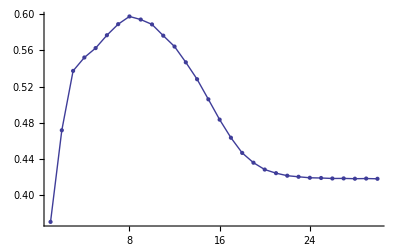

```mathematica
ListPlot[Map[Sz2,Range[NMAX]],Joined->True,PlotRange->All,Mesh->All]
```

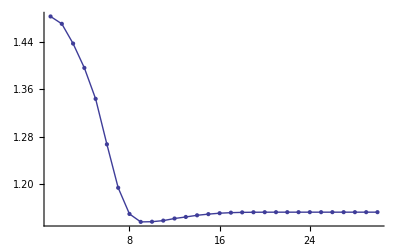

```mathematica
ListPlot[Map[expv[#,"nd2"]&,Range[NMAX]],Joined->True,PlotRange->All,Mesh->All]
```

```mathematica
spaghetti[nmax_,levels_,start_:1]:=Reverse/@Flatten[Table[Riffle[Take[energies[n],levels],n]~Partition~2,{n,start,nmax,2}],1];
```

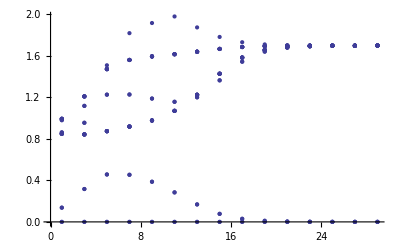

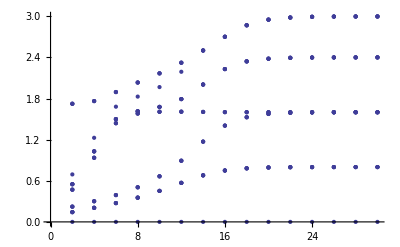

```mathematica
ListPlot[spaghetti[NMAX,20,1]]
ListPlot[spaghetti[NMAX,20,2]]
```